```mathematica
With[
{tupleList = Subsets[Prime[Range[2,11]], {2,15}],
range=15000},
Monitor[Table[
With[
{tuple=tupleList[[tuplePos]]},
With [{votes= DynamicVoteList[tuple,range]},

(*PrintTemporary[ToString[tuple] <> " ---> " <> ToString[tuplePos] <> " / " <> ToString[Length[tupleList]]];*)
{N[magicGraham[tuple]], N[Log[Last[votes] [[1]]   ]]}
]
]
, {tuplePos,1,Length[ tupleList]}
], ToString[tupleList[[tuplePos]]] <> " ---> "  <> ToString[tuplePos] <> " / " <> ToString[Length[tupleList]]
]
]
```

$Aborted

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2],InputStream[d:\triangle\Votes\3\5\13\19\29\Votes.txt,385],InputStream[d:\triangle\Votes\3\5\19\23\Votes.txt,524],InputStream[d:\triangle\Votes\5\7\11\17\31\Votes.txt,5647197]}

```mathematica
Close[Streams[][[3]]]
```

Close[{OutputStream[stdout,1],OutputStream[stderr,2]}⟦3⟧]

```mathematica
all=%
```

{{0.313536,21.2671},{0.343344,20.1768},{0.378151,17.6186},{0.389584,16.5966},{0.406454,17.7284},{0.412941,17.7212},{0.423439,16.7761},{0.435151,15.7857},{0.395021,17.7959},{0.429828,16.8114},{0.441261,16.2929},{0.45813,15.3967},{0.464618,14.8882},{0.475115,14.851},{0.486827,14.8901},{0.459636,15.6109},{0.471069,15.628},{0.487938,14.8682},{0.494426,13.9043},{0.504923,14.0229},{0.516635,14.3396},{0.505876,14.5151},{0.522746,14.43},{0.529233,13.5996},{0.539731,13.6693},{0.551443,13.6395},{0.534178,14.2911},{0.540666,13.606},{0.551163,13.7401},{0.562875,13.6377},{0.557535,13.1655},{0.568033,13.2985},{0.579745,12.5442},{0.57452,13.2429},{0.586233,12.6264},{0.59673,12.6835},{0.0259503,100.016},{0.0607577,53.1295},{0.0721904,45.4137},{0.0890598,48.4807},{0.0955474,44.27},{0.106045,41.0288},{0.117757,41.9002},{0.0905659,48.7078},{0.101999,41.0528},{0.118868,39.6899},{0.125356,43.2149},{0.135853,35.3096},{0.147565,36.2597},{0.136806,36.2908},{0.153675,37.6682},{0.160163,37.4706},{0.17066,28.957},{0.182373,32.0016},{0.165108,30.0315},{0.171596,30.8828},{0.182093,28.618},{0.193805,31.1302},{0.188465,27.6179},{0.198962,27.5058},{0.210675,25.5661},{0.20545,26.5169},{0.217162,25.5562},{0.22766,28.5818},{0.142242,36.218},{0.153675,32.247},{0.170544,32.3804},{0.177032,31.3931},{0.187529,27.4001},{0.199242,28.0823},{0.188482,29.8848},{0.205352,29.1686},{0.211839,27.6216},{0.222337,26.5446},{0.234049,27.7656},{0.216784,24.5359},{0.223272,26.5648},{0.233769,25.8091},{0.245482,25.7994},{0.240142,24.3324},{0.250639,23.429},{0.262351,22.7803},{0.257126,22.7491},{0.268839,21.0162},{0.279336,24.3659},{0.218291,26.4891},{0.23516,26.4094},{0.241648,27.2457},{0.252145,24.066},{0.263857,21.7075},{0.246593,23.4199},{0.25308,22.3126},{0.263578,22.3126},{0.27529,22.3177},{0.26995,24.4707},{0.280447,23.3606},{0.292159,21.675},{0.286935,19.6288},{0.298647,22.2929},{0.309144,22.1893},{0.2814,21.9626},{0.287888,20.8537},{0.298385,20.8147},{0.310097,20.6002},{0.304757,20.6661},{0.315254,20.6204},{0.326967,21.6756},{0.321742,20.6362},{0.333454,19.4951},{0.343952,17.6913},{0.31619,20.6172},{0.326687,20.6155},{0.338399,18.658},{0.333175,19.0573},{0.344887,18.8368},{0.355384,19.0574},{0.350044,19.0792},{0.361756,18.4883},{0.372254,18.8139},{0.378741,17.9945},{-0.226828,1166.86},{-0.215395,1154.92},{-0.198526,1028.68},{-0.192038,1061.41},{-0.181541,966.048},{-0.169829,926.268},{-0.180588,996.6},{-0.163718,915.144},{-0.157231,905.405},{-0.146734,795.408},{-0.135021,775.94},{-0.152286,847.318},{-0.145798,883.729},{-0.135301,721.936},{-0.123589,702.119},{-0.128929,723.331},{-0.118431,733.914},{-0.106719,634.998},{-0.111944,670.259},{-0.100232,587.445},{-0.0897342,639.392},{-0.15078,825.207},{-0.13391,777.116},{-0.127423,792.237},{-0.116925,687.04},{-0.105213,679.314},{-0.122478,718.886},{-0.11599,658.445},{-0.105493,627.309},{-0.0937804,564.289},{-0.0991205,641.59},{-0.0886232,518.711},{-0.0769109,426.413},{-0.0821356,524.363},{-0.0704233,508.462},{-0.0599261,455.924},{-0.0876702,573.919},{-0.0811826,499.085},{-0.0706853,451.699},{-0.058973,322.033},{-0.0643132,448.406},{-0.0538159,368.333},{-0.0421036,264.875},{-0.0473283,356.277},{-0.035616,239.903},{-0.0251187,160.695},{-0.0528805,316.441},{-0.0423832,175.831},{-0.0306709,215.729},{-0.0358956,237.407},{-0.0241833,198.97},{-0.013686,139.92},{-0.0190261,142.82},{-0.00731384,107.983},{0.00318344,92.3204},{0.00967106,90.1279},{-0.0991033,565.141},{-0.0822338,576.393},{-0.0757462,401.561},{-0.0652489,366.132},{-0.0535366,230.38},{-0.0708011,487.679},{-0.0643135,441.878},{-0.0538163,301.773},{-0.042104,288.783},{-0.0474441,343.208},{-0.0369468,261.447},{-0.0252345,187.066},{-0.0304592,224.587},{-0.0187469,175.828},{-0.00824961,125.791},{-0.0359938,232.639},{-0.0295062,219.69},{-0.0190089,123.929},{-0.0072966,188.703},{-0.0126367,127.847},{-0.00213943,152.167},{0.00957285,94.9976},{0.00434818,108.088},{0.0160605,75.7239},{0.0265578,90.2162},{-0.00120404,146.476},{0.00929324,91.0253},{0.0210055,71.0622},{0.0157809,85.5498},{0.0274931,95.0486},{0.0379904,59.8098},{0.0326503,70.8358},{0.0443626,51.6982},{0.0548599,58.6763},{0.0613475,55.1195},{-0.00618561,109.133},{0.000302007,152.172},{0.0107993,82.9632},{0.0225116,82.9253},{0.0171715,97.5626},{0.0276687,63.5092},{0.039381,62.4548},{0.0341564,79.8284},{0.0458686,72.1335},{0.0563659,61.4228},{0.0286041,66.8573},{0.0391014,67.0141},{0.0508137,54.6405},{0.045589,64.9314},{0.0573013,54.6745},{0.0677986,44.},{0.0624585,60.6805},{0.0741708,49.3445},{0.0846681,45.6006},{0.0911557,45.8682},{0.0634115,56.8334},{0.0739088,57.8619},{0.0856211,41.1417},{0.0803964,50.3762},{0.0921087,48.},{0.102606,48.8257},{0.0972659,47.1734},{0.108978,45.5957},{0.119475,41.5232},{0.125963,38.4853},{0.108699,39.9391},{0.120411,37.1529},{0.130908,38.5036},{0.137396,34.4961},{0.154265,31.5566},{-0.468174,1746.24},{-0.451304,1679.32},{-0.444816,1673.82},{-0.434319,1636.93},{-0.422607,1639.87},{-0.439871,1683.21},{-0.433384,1623.75},{-0.422886,1619.36},{-0.411174,1606.57},{-0.416514,1609.62},{-0.406017,1592.83},{-0.394305,1538.06},{-0.399529,1571.08},{-0.387817,1537.28},{-0.37732,1545.94},{-0.405064,1531.27},{-0.398576,1575.97},{-0.388079,1499.08},{-0.376367,1522.02},{-0.381707,1508.45},{-0.37121,1476.53},{-0.359497,1434.8},{-0.364722,1481.11},{-0.35301,1442.78},{-0.342512,1422.82},{-0.370274,1488.13},{-0.359777,1457.23},{-0.348065,1389.02},{-0.353289,1452.53},{-0.341577,1436.98},{-0.33108,1368.93},{-0.33642,1408.42},{-0.324708,1326.18},{-0.31421,1357.88},{-0.307723,1315.25},{-0.375256,1463.41},{-0.368768,1458.28},{-0.358271,1456.23},{-0.346559,1410.9},{-0.351899,1442.48},{-0.341402,1387.55},{-0.329689,1401.83},{-0.334914,1378.91},{-0.323202,1360.5},{-0.312704,1353.49},{-0.340466,1384.3},{-0.329969,1362.14},{-0.318257,1294.03},{-0.323481,1333.85},{-0.311769,1302.22},{-0.301272,1286.65},{-0.306612,1342.94},{-0.294899,1256.},{-0.284402,1240.33},{-0.277915,1207.91},{-0.305659,1290.36},{-0.295161,1266.74},{-0.283449,1183.21},{-0.288674,1234.03},{-0.276962,1180.72},{-0.266464,1097.42},{-0.271804,1208.83},{-0.260092,1157.21},{-0.249595,1075.87},{-0.243107,1086.67},{-0.260372,1140.45},{-0.248659,1103.29},{-0.238162,1068.15},{-0.231675,994.262},{-0.214805,995.349},{-0.323579,1321.97},{-0.317092,1281.52},{-0.306595,1263.81},{-0.294882,1227.08},{-0.300222,1209.78},{-0.289725,1217.44},{-0.278013,1185.46},{-0.283237,1161.1},{-0.271525,1146.89},{-0.261028,1167.77},{-0.28879,1219.},{-0.278292,1215.13},{-0.26658,1131.14},{-0.271805,1183.11},{-0.260092,1072.58},{-0.249595,1111.4},{-0.254935,1134.65},{-0.243223,1014.98},{-0.232726,1049.68},{-0.226238,1001.07},{-0.253982,1023.41},{-0.243485,1038.29},{-0.231773,1015.},{-0.236997,994.633},{-0.225285,958.431},{-0.214788,935.266},{-0.220128,958.444},{-0.208416,890.362},{-0.197918,853.002},{-0.191431,839.35},{-0.208695,915.83},{-0.196983,845.396},{-0.186486,829.254},{-0.179998,821.689},{-0.163129,808.168},{-0.224174,931.248},{-0.213677,913.815},{-0.201965,845.255},{-0.207189,901.728},{-0.195477,867.096},{-0.18498,808.284},{-0.19032,845.757},{-0.178607,808.28},{-0.16811,775.307},{-0.161623,775.272},{-0.178887,741.999},{-0.167175,698.64},{-0.156678,722.469},{-0.15019,716.367},{-0.13332,691.997},{-0.14408,676.373},{-0.132367,524.425},{-0.12187,616.511},{-0.115383,595.068},{-0.0985131,504.312},{-0.0870804,402.697},{-0.69265,1996.63},{-0.686162,1998.1},{-0.675665,1976.4},{-0.663952,1998.45},{-0.669293,1953.86},{-0.658795,1955.72},{-0.647083,1946.3},{-0.652308,1946.27},{-0.640595,1938.46},{-0.630098,1927.19},{-0.65786,1948.94},{-0.647363,1962.82},{-0.63565,1936.85},{-0.640875,1916.02},{-0.629163,1903.19},{-0.618665,1913.78},{-0.624006,1913.11},{-0.612293,1862.44},{-0.601796,1885.22},{-0.595308,1863.25},{-0.623053,1876.81},{-0.612555,1854.77},{-0.600843,1830.26},{-0.606068,1844.67},{-0.594355,1861.05},{-0.583858,1822.6},{-0.589198,1814.02},{-0.577486,1796.38},{-0.566989,1788.92},{-0.560501,1775.36},{-0.577766,1816.72},{-0.566053,1805.02},{-0.555556,1785.24},{-0.549068,1761.42},{-0.532199,1735.81},{-0.593244,1829.19},{-0.582747,1816.32},{-0.571035,1789.64},{-0.576259,1828.5},{-0.564547,1802.2},{-0.55405,1782.64},{-0.55939,1801.07},{-0.547678,1796.27},{-0.53718,1757.98},{-0.530693,1746.79},{-0.547957,1780.07},{-0.536245,1723.72},{-0.525748,1732.96},{-0.51926,1714.35},{-0.502391,1679.78},{-0.51315,1678.72},{-0.501438,1652.31},{-0.49094,1615.25},{-0.484453,1593.11},{-0.467583,1576.51},{-0.456151,1540.63},{-0.541568,1669.59},{-0.531071,1672.21},{-0.519358,1660.26},{-0.524583,1644.13},{-0.512871,1621.08},{-0.502373,1633.14},{-0.507714,1632.62},{-0.496001,1574.03},{-0.485504,1596.56},{-0.479016,1568.47},{-0.496281,1602.47},{-0.484569,1540.36},{-0.474071,1568.4},{-0.467584,1550.89},{-0.450714,1509.65},{-0.461474,1487.84},{-0.449761,1486.08},{-0.439264,1458.33},{-0.432776,1421.95},{-0.415907,1416.31},{-0.404474,1389.03},{-0.431665,1431.24},{-0.419953,1388.55},{-0.409456,1377.7},{-0.402968,1394.39},{-0.386099,1338.03},{-0.374666,1291.09},{-0.339859,1167.28},{-0.910638,2175.53},{-0.900141,2182.4},{-0.888429,2176.35},{-0.893653,2165.8},{-0.881941,2174.15},{-0.871444,2170.1},{-0.876784,2146.12},{-0.865072,2133.41},{-0.854574,2126.99},{-0.848087,2125.81},{-0.865351,2158.97},{-0.853639,2122.99},{-0.843142,2137.9},{-0.836654,2112.63},{-0.819785,2095.05},{-0.830544,2060.35},{-0.818831,2050.68},{-0.808334,2032.9},{-0.801847,2030.24},{-0.784977,2007.16},{-0.773544,2006.72},{-0.800736,2062.1},{-0.789023,2024.04},{-0.778526,2028.66},{-0.772038,2028.72},{-0.755169,2012.66},{-0.743736,1986.08},{-0.708929,1892.93},{-0.749059,1923.28},{-0.737347,1902.52},{-0.72685,1912.65},{-0.720362,1878.95},{-0.703493,1867.23},{-0.69206,1843.67},{-0.657252,1746.93},{-0.627444,1722.13},{-1.11813,2309.07},{-1.10642,2298.48},{-1.09592,2301.45},{-1.08943,2297.49},{-1.07256,2267.7},{-1.06113,2269.98},{-1.02632,2192.11},{-0.996515,2197.98},{-0.944838,2084.36},{-1.31391,2396.9}}

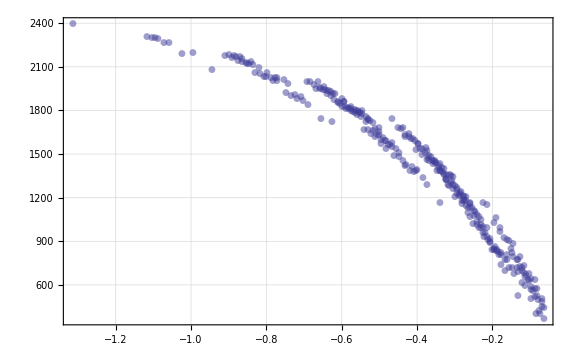

```mathematica
ListPlot[Sort[all], 
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
FrameLabel->"Tuple magic value vs Ln of nth voted value\nFor 1000th voted value",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->Large,
PlotRange->All,
PlotStyle->Opacity[0.5]
]
```

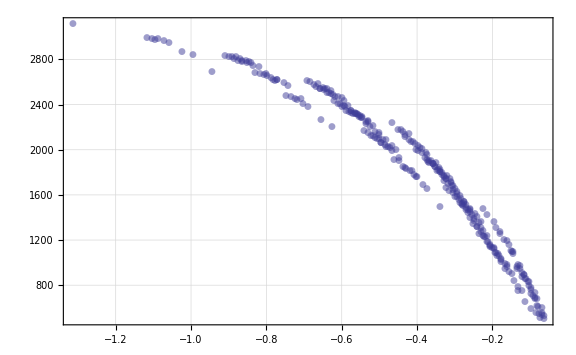

```mathematica
ListPlot[Sort[all], 
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Log 10 of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
FrameLabel->"Tuple magic value vs Log10 of nth voted value\nFor 15000th voted value",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->Large,
PlotRange->All,
PlotStyle->Opacity[0.5]
]
```

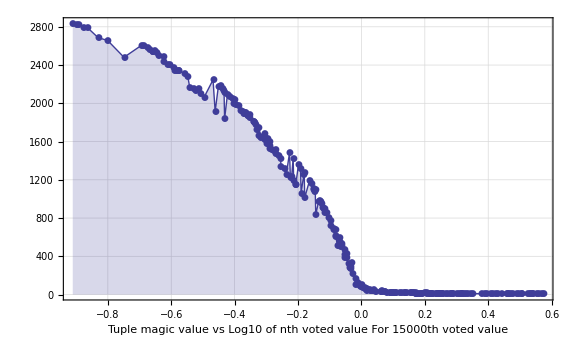

```mathematica
ListLinePlot[Sort[all], 
PlotMarkers->Automatic, 
Filling->Axis, 
AxesLabel->{"magic Graham for tuple", "Log 10 of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
FrameLabel->"Tuple magic value vs Log10 of nth voted value\nFor 15000th voted value",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->Large
]
```